```mathematica
ClearAll["Global`*"]
```

## Parameters

```mathematica
e=1.60 10^-19;
m=6.65 10^-26;
Ω=6 10^9;
r0=3 10^-3;
V0=200;
U0=1 10^-6;
β=5 10^-3;
Tmax=30000;
a[e_,U0_,m_,r0_,Ω_]:=(4 e U0)/(m r0^4 Ω^2)
q[e_,V0_,m_,r0_,Ω_]:=(2 e V0)/(m r0^4 Ω^2)
```

## Equations

```mathematica
ζ4a=x[τ]^4-3 x[τ]^2 y[τ]^2-3 x[τ]^2 z[τ]^2+3 y[τ]^2 z[τ]^2;
ζ4b=z[τ]y[τ](z[τ]^2-3 x[τ]^2);
GradXofζ4a=D[-ζ4a,x[τ]];
GradYofζ4a=D[-ζ4a,y[τ]];
GradZofζ4a=D[-ζ4a,z[τ]];
GradXofζ4b=D[-ζ4b,x[τ]];
GradYofζ4b=D[-ζ4b,y[τ]];
GradZofζ4b=D[-ζ4b,z[τ]];
EqsForζ4a[U0_,β_]:={x''[τ]==(a[e,U0,m,r0,Ω]+2 q [e,V0,m,r0,Ω]Cos[2τ])GradXofζ4a-β x'[τ],
y''[τ]==(a[e,U0,m,r0,Ω]+2q [e,V0,m,r0,Ω] Cos[2τ])GradYofζ4a-β y'[τ],
z''[τ]==(a[e,U0,m,r0,Ω]+2 q [e,V0,m,r0,Ω] Cos[2τ])GradZofζ4a-β z'[τ]};
EqsForζ4b[U0_,β_]:={x''[τ]==(a[e,U0,m,r0,Ω]+2 q [e,V0,m,r0,Ω] Cos[2τ])GradXofζ4b-β x'[τ],
y''[τ]==(a[e,U0,m,r0,Ω]+2 q [e,V0,m,r0,Ω] Cos[2τ])GradYofζ4b-β y'[τ],
z''[τ]==(a[e,U0,m,r0,Ω]+2 q [e,V0,m,r0,Ω] Cos[2τ])GradZofζ4b-β z'[τ]};
InValues={x[0]==0.01,y[0]==0.01,z[0]==0.01,x'[0]==0.001,y'[0]==0.001,z'[0]==0.001};
Varibles={x,y,z};
Soln[EqsForWhat_,U0_,β_]:=NDSolveValue[{EqsForWhat[U0,β],InValues,WhenEvent[√(x[τ]^2+y[τ]^2+z[τ]^2)≥1,"StopIntegration"]},Varibles,{τ,0,Tmax}];
```

```mathematica
solnζ4a=Soln[EqsForζ4a,U0,0.09β];
solnζ4b=Soln[EqsForζ4b,U0,0.09β];
finalTimeζ4a=solnζ4a[[1,1,1,2]];
finalTimeζ4b=solnζ4b[[1,1,1,2]];
```

final time for ζ4a: | 30000.
final time for ζ4b: | 30000.

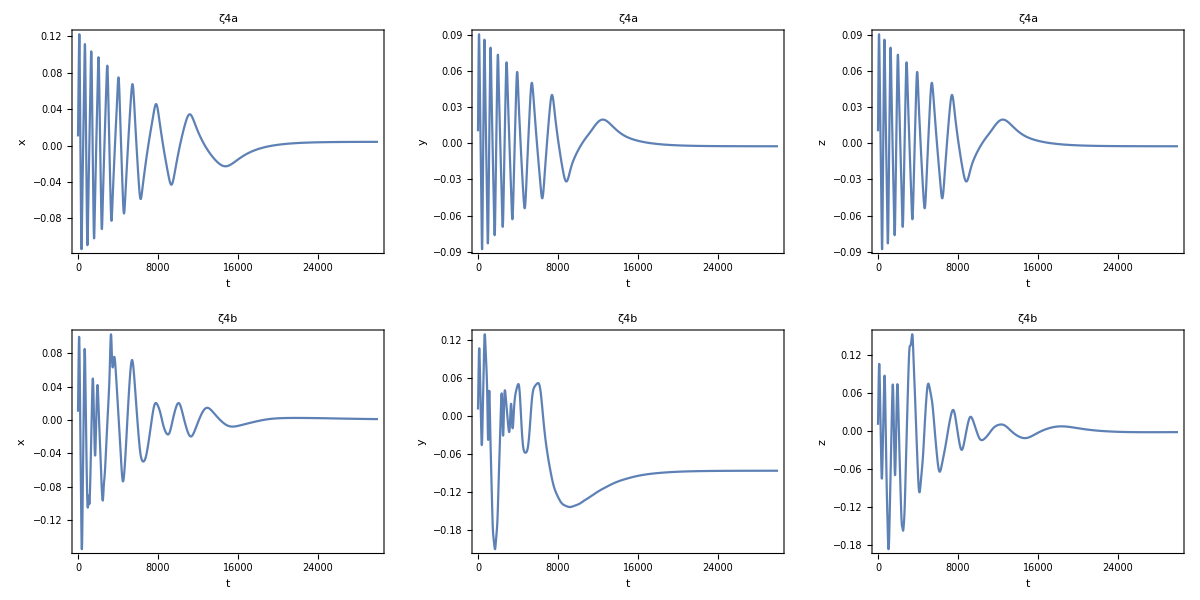

-Graphics3D-

-Graphics3D-

```mathematica
TableForm[{{"final time for ζ4a:",finalTimeζ4a},{"final time for ζ4b:",finalTimeζ4b}}]
TableForm[{{Plot[solnζ4a[[1]][t],{t,0,finalTimeζ4a},PlotRange->All,AxesLabel->{Style["t",Black,14],Style["x",Black,14]},PlotLabel->Style["ζ4a",Black,20],Frame->True],
Plot[solnζ4a[[2]][t],{t,0,finalTimeζ4a},PlotRange->All,AxesLabel->{Style["t",Black,14],Style["y",Black,14]},PlotLabel->Style["ζ4a",Black,20],Frame->True],
Plot[solnζ4a[[3]][t],{t,0,finalTimeζ4a},PlotRange->All,AxesLabel->{Style["t",Black,14],Style["z",Black,14]},PlotLabel->Style["ζ4a",Black,20],Frame->True]},{
Plot[solnζ4b[[1]][t],{t,0,finalTimeζ4b},PlotRange->All,AxesLabel->{Style["t",Black,14],Style["x",Black,14]},PlotLabel->Style["ζ4b",Black,20],Frame->True],
Plot[solnζ4b[[2]][t],{t,0,finalTimeζ4b},PlotRange->All,AxesLabel->{Style["t",Black,14],Style["y",Black,14]},PlotLabel->Style["ζ4b",Black,20],Frame->True],
Plot[solnζ4b[[3]][t],{t,0,finalTimeζ4b},PlotRange->All,AxesLabel->{Style["t",Black,14],Style["z",Black,14]},PlotLabel->Style["ζ4b",Black,20],Frame->True]}}]
Show[ParametricPlot3D[{solnζ4a[[1]][τ],solnζ4a[[2]][τ],solnζ4a[[3]][τ]},{τ,0,finalTimeζ4a},PlotRange->All,AspectRatio->1],Graphics3D[{Red,PointSize[0.05],Point[{solnζ4a[[1]][finalTimeζ4a],solnζ4a[[2]][finalTimeζ4a],solnζ4a[[3]][finalTimeζ4a]}]}]]
Show[ParametricPlot3D[{solnζ4b[[1]][τ],solnζ4b[[2]][τ],solnζ4b[[3]][τ]},{τ,0,finalTimeζ4b},PlotRange->All,AspectRatio->1],Graphics3D[{Red,PointSize[0.05],Point[{solnζ4b[[1]][finalTimeζ4b],solnζ4b[[2]][finalTimeζ4b],solnζ4b[[3]][finalTimeζ4b]}]}]]
```